# Pêndulo livre com controlo, com Runge-Kutta 4.aa ordem

```mathematica
ClearAll["Global`*"]
ClearAll[Subscript]
ClearAll[Derivative]
SetSystemOptions["SimplificationOptions"->"AutosimplifyTrigs"->False];
```

## Introdução de variáveis e funções de controlo

```mathematica
x[t_]:=fx[t]+l Cos[ϕ[t]]Sin[θ[t]];
y[t_]:=fy[t]+l Sin[ϕ[t]]Sin[θ[t]];
z[t_]:=l Cos[θ[t]];
```

## Lagrangeano do Pêndulo esférico com controlo

```mathematica
L=1/2 m(D[x[t],t]^2+D[y[t],t]^2+D[z[t],t]^2)-m g z[t]//FullSimplify;
```

## Equação de movimento

```mathematica
Substeta=First[Solve[D[D[L,θ'[t]],t]-D[L,θ[t]]==0,θ''[t]]//FullSimplify]
Subsphi=First[Solve[D[D[L,ϕ'[t]],t]-D[L,ϕ[t]]==0,ϕ''[t]]//FullSimplify]
Solve[D[D[L,fx'[t]],t]-D[L,fx[t]]==0/.Substeta/.Subsphi,fx''[t]]//FullSimplify
```

{θ''[t]→(g Sin[θ[t]]+Cos[θ[t]] (l Sin[θ[t]] ϕ'[t]^2-Cos[ϕ[t]] fx''[t]-Sin[ϕ[t]] fy''[t]))/l}

{ϕ''[t]→(Csc[θ[t]] (-2 l Cos[θ[t]] θ'[t] ϕ'[t]+Sin[ϕ[t]] fx''[t]-Cos[ϕ[t]] fy''[t]))/l}

{{fx''[t]→Csc[θ[t]] Sec[ϕ[t]] (-g Cos[θ[t]]+l θ'[t]^2+l Sin[θ[t]]^2 ϕ'[t]^2-Sin[θ[t]] Sin[ϕ[t]] fy''[t])}}

## Energia sem controlo

```mathematica
H=1/2 m(x'[t]^2+y'[t]^2+z'[t]^2)+m g z[t] /.{fy[t]->0,fx[t]->0,fx'[t]->0,fy'[t]->0}//FullSimplify
```

1/2 l m (2 g Cos[θ[t]]+l θ'[t]^2+l Sin[θ[t]]^2 ϕ'[t]^2)

```mathematica
Subscript[E, 1]=H/.θ[t]->0/.θ'[t]->0
```

g l m

## Controlo

```mathematica
(*EqsH={pθ'[t]->-D[H1,θ[t]], pϕ'[t]->-D[H1,ϕ[t]], θ'[t]->D[H1,pθ[t]], ϕ'[t]->D[H1,pϕ[t]]}//FullSimplify;*)
```

```mathematica
(*D[H,t]/.EqsH//FullSimplify*)
```

### Derivada da energia com as equações de movimento substituidas

```mathematica
D[H,t]/.Substeta/.Subsphi//FullSimplify
```

-l m (Sin[θ[t]] ϕ'[t] (-Sin[ϕ[t]] fx''[t]+Cos[ϕ[t]] fy''[t])+Cos[θ[t]] θ'[t] (Cos[ϕ[t]] fx''[t]+Sin[ϕ[t]] fy''[t]))

```mathematica
C1=D[H,t]/.Substeta/.Subsphi /.fy''[t]->fx''[t] Tan[ϕ[t]]/.fx''[t]->u Cos [ϕ[t]]l   //FullSimplify
```

-l^2 m u Cos[θ[t]] θ'[t]

```mathematica
C2=D[H,t]/.Substeta/.Subsphi/.fx''[t]->-fy''[t] Tan[ϕ[t]]/.fy''[t]->v Cos[ϕ[t]] l//FullSimplify//TrigFactor
```

-l^2 m v Sin[θ[t]] ϕ'[t]

### Parametros Físicos

```mathematica
paramFis={m->1,g->1,l->1,μ->0.2,ν->0.2};
```

## Integração numérica

## Equações do movimento

#### Parametros numéricos

```mathematica
Δt=0.001;
nMAX=25000;
```

## Integração de θ̇, e ϕ̇ por Runge-Kutta 4.aa ordem e ϕ, θ por Euler

```mathematica
For[Subscript[θ, RK4][0]=π/2;Subscript[θ, RK4]'[0]=-0.5;Subscript[ϕ, RK4][0]=0;Subscript[ϕ, RK4]'[0]=1;i2=0;i=0;v1x[0]=0;v1y[0]=0;Subscript[x1, RK4][0]=0;Subscript[y1, RK4][0]=0,i<nMAX,i++,
If[i==0,Print[i]];
(*percentagem*)
If[(i-i2)/nMAX>0.1,Print[N[i*100/nMAX]];i2=i];

(*Funções de controlo u e v*)
Subscript[u, RK4][i]=-μ  Sign[Subscript[E, 1]-H] Sign[C1/(-m l^2 u)]/.{θ'[t]->Subscript[θ, RK4]'[i],θ[t]->Subscript[θ, RK4][i],ϕ'[t]->Subscript[ϕ, RK4]'[i],ϕ[t]->Subscript[ϕ, RK4][i]}/.paramFis;
(*Subscript[u, RK4][i]=-μ  (Subscript[E, 1]-H) (C1/(-m l^2 u))/.{θ'[t]->Subscript[θ, RK4]'[i],θ[t]->Subscript[θ, RK4][i],ϕ'[t]->Subscript[ϕ, RK4]'[i],ϕ[t]->Subscript[ϕ, RK4][i]}/.paramFis;*)

Subscript[ux, RK4][i]=Subscript[u, RK4][i] Cos[Subscript[ϕ, RK4][i]];
Subscript[v, RK4][i]=ν  Sign[C2/(-m l^2 v)]/.{θ'[t]->Subscript[θ, RK4]'[i],θ[t]->Subscript[θ, RK4][i],ϕ'[t]->Subscript[ϕ, RK4]'[i],ϕ[t]->Subscript[ϕ, RK4][i]}/.paramFis;
(*Subscript[v, RK4][i]=ν  C2/(-m l^2 v)/.{θ'[t]->Subscript[θ, RK4]'[i],θ[t]->Subscript[θ, RK4][i],ϕ'[t]->Subscript[ϕ, RK4]'[i],ϕ[t]->Subscript[ϕ, RK4][i]}/.paramFis;*)
Subscript[vy, RK4][i]=Subscript[v, RK4][i] Cos[Subscript[ϕ, RK4][i]];


A0={fx''[t]->fx1''[t]+fx2''[t],fy''[t]->fy1''[t]+fy2''[t]};
A1={fy1''[t]->fx1''[t]Tan[ϕ[t]],fx2''[t]->-fy2''[t]Tan[ϕ[t]]} ;
A2={fx1''[t]->l Subscript[ux, RK4][i],fy2''[t]->l Subscript[vy, RK4][i]};
ax[i]=Subscript[ux, RK4][i]-Subscript[vy, RK4][i]Tan[Subscript[ϕ, RK4][i]];
ay[i]=Subscript[ux, RK4] [i]Tan[Subscript[ϕ, RK4][i]]+Subscript[vy, RK4][i];


(*Runge-kutta para θ''[t]*)
fθ[i]=θ''[t]/.Substeta/.A0/.A1/.A2/.{θ'[t]->Subscript[θ, RK4]'[i],θ[t]->Subscript[θ, RK4][i],ϕ'[t]->Subscript[ϕ, RK4]'[i],ϕ[t]->Subscript[ϕ, RK4][i]}/.paramFis;

K1=fθ[i];
K2=fθ[i]/.{Subscript[θ, RK4]'[i]->Subscript[θ, RK4]'[i]+Δt/2 K1,Subscript[θ, RK4][i]->Subscript[θ, RK4][i]+Δt/2 K1,Subscript[ϕ, RK4]'[i]->Subscript[ϕ, RK4]'[i]+Δt/2 K1,Subscript[ϕ, RK4][i]->Subscript[ϕ, RK4][i]+Δt/2 K1,Subscript[ux, RK4][i]->Subscript[ux, RK4][i]+Δt/2 K1,Subscript[vy, RK4][i]->Subscript[vy, RK4][i]+Δt/2 K1};
K3=fθ[i]/.{Subscript[θ, RK4]'[i]->Subscript[θ, RK4]'[i]+Δt/2 K2,Subscript[θ, RK4][i]->Subscript[θ, RK4][i]+Δt/2 K2,Subscript[ϕ, RK4]'[i]->Subscript[ϕ, RK4]'[i]+Δt/2 K2,Subscript[ϕ, RK4][i]->Subscript[ϕ, RK4][i]+Δt/2 K2,Subscript[ux, RK4][i]->Subscript[ux, RK4][i]+Δt/2 K2,Subscript[vy, RK4][i]->Subscript[vy, RK4][i]+Δt/2 K2};
K4=fθ[i]/.{Subscript[θ, RK4]'[i]->Subscript[θ, RK4]'[i]+Δt K3,Subscript[θ, RK4][i]->Subscript[θ, RK4][i]+Δt K3,Subscript[ϕ, RK4]'[i]->Subscript[ϕ, RK4]'[i]+Δt K3,Subscript[ϕ, RK4][i]->Subscript[ϕ, RK4][i]+Δt K3,Subscript[ux, RK4][i]->Subscript[ux, RK4][i]+Δt K3,Subscript[vy, RK4][i]->Subscript[vy, RK4][i]+Δt K3};


(*Runge-kutta para ϕ''[t]*)
fϕ[i]=ϕ''[t]/.Subsphi/.A0/.A1/.A2/.{θ'[t]->Subscript[θ, RK4]'[i],θ[t]->Subscript[θ, RK4][i],ϕ'[t]->Subscript[ϕ, RK4]'[i],ϕ[t]->Subscript[ϕ, RK4][i]}/.paramFis;
G1=fϕ[i];
G2=fϕ[i]/.{Subscript[θ, RK4]'[i]->Subscript[θ, RK4]'[i]+Δt/2 K1,Subscript[θ, RK4][i]->Subscript[θ, RK4][i]+Δt/2 K1,Subscript[ϕ, RK4]'[i]->Subscript[ϕ, RK4]'[i]+Δt/2 K1,Subscript[ϕ, RK4][i]->Subscript[ϕ, RK4][i]+Δt/2 K1,Subscript[ux, RK4][i]->Subscript[ux, RK4][i]+Δt/2 K1,Subscript[vy, RK4][i]->Subscript[vy, RK4][i]+Δt/2 K1};
G3=fϕ[i]/.{Subscript[θ, RK4]'[i]->Subscript[θ, RK4]'[i]+Δt/2 K2,Subscript[θ, RK4][i]->Subscript[θ, RK4][i]+Δt/2 K2,Subscript[ϕ, RK4]'[i]->Subscript[ϕ, RK4]'[i]+Δt/2 K2,Subscript[ϕ, RK4][i]->Subscript[ϕ, RK4][i]+Δt/2 K2,Subscript[ux, RK4][i]->Subscript[ux, RK4][i]+Δt/2 K2,Subscript[vy, RK4][i]->Subscript[vy, RK4][i]+Δt/2 K2};
G4=fϕ[i]/.{Subscript[θ, RK4]'[i]->Subscript[θ, RK4]'[i]+Δt K3,Subscript[θ, RK4][i]->Subscript[θ, RK4][i]+Δt K3,Subscript[ϕ, RK4]'[i]->Subscript[ϕ, RK4]'[i]+Δt K3,Subscript[ϕ, RK4][i]->Subscript[ϕ, RK4][i]+Δt K3,Subscript[ux, RK4][i]->Subscript[ux, RK4][i]+Δt K3,Subscript[vy, RK4][i]->Subscript[vy, RK4][i]+Δt K3};


(*Próxima iteração*)
Subscript[θ, RK4]'[i+1]=Subscript[θ, RK4]'[i]+Δt/6(K1 +2 K2+2 K3+K4);
Subscript[θ, RK4][i+1]=Subscript[θ, RK4]'[i]Δt+Subscript[θ, RK4][i];
Subscript[ϕ, RK4]'[i+1]=Subscript[ϕ, RK4]'[i]+Δt/6(G1+2 G2+2 G3+G4);
Subscript[ϕ, RK4][i+1]=Subscript[ϕ, RK4]'[i] Δt + Subscript[ϕ, RK4][i];

v1x[i+1]=v1x[i]+ax[i] Δt;
v1y[i+1]=v1y[i]+ay[i] Δt;
Subscript[x1, RK4][i+1]=Subscript[x1, RK4][i]+v1x[i] Δt;
Subscript[y1, RK4][i+1]=Subscript[y1, RK4][i]+v1y[i] Δt;

(*Condições Fronteira*)
If[Subscript[θ, RK4][i+1]>π,Subscript[ϕ, RK4][i+1]=Subscript[ϕ, RK4][i+1]+π;Subscript[θ, RK4][i+1]=2π-Subscript[θ, RK4][i+1];Subscript[θ, RK4]'[i+1]=-Subscript[θ, RK4]'[i+1]];

If[Subscript[θ, RK4][i+1]<0,Subscript[ϕ, RK4][i+1]=Subscript[ϕ, RK4][i+1]+π ;  Subscript[θ, RK4][i+1]=-Subscript[θ, RK4][i+1] ; Subscript[θ, RK4]'[i+1]=-Subscript[θ, RK4]'[i+1]]]
```

0

10.004

20.008

30.012

40.016

50.02

60.024

70.028

80.032

90.036

## Resultados

```mathematica
(*Animate[Show[{Graphics3D[{Opacity[0.2],Sphere[{0,0,0}]}],{ListPointPlot3D[Table[{Cos[Subscript[ϕ, RK4][n]] Sin[Subscript[θ, RK4][n]],Sin[Subscript[ϕ, RK4][n]] Sin[Subscript[θ, RK4][n]],Cos[Subscript[θ, RK4][n]]},{n,0,n1,100}]]}}],{n1,0,nMAX,100},DefaultDuration->30,AnimationRunning->False]*)
```

```mathematica
(*Animate[Show[{Graphics3D[{Opacity[0.2],Sphere[{0,0,0}]}],{ListPointPlot3D[{{Cos[Subscript[ϕ, RK4][n]] Sin[Subscript[θ, RK4][n]],Sin[Subscript[ϕ, RK4][n]] Sin[Subscript[θ, RK4][n]],Cos[Subscript[θ, RK4][n]]}}]}}],{n,0,nMAX,100},DefaultDuration->30,AnimationRunning->False]*)
```

## Referencial Laboratório

```mathematica
Animate[Append[Show[Graphics3D[{Opacity[0.2],Sphere[{Subscript[x1, RK4][n],Subscript[y1, RK4][n],0}]}],Graphics3D[{Red,Arrow[{{0,0,0},{1.5,0,0}}]}],Graphics3D[{Red,Arrow[{{0,0,0},{0,1.5,0}}]}],Graphics3D[{Red,Arrow[{{0,0,0},{0,0,1.5}}]}](*,Graphics3D[{Red,Arrow[{{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]},{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]]-Cos[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]]-Cos[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]+Sin[Subscript[θ, RK4][n]]}}]}],Graphics3D[{Red,Arrow[{{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]},{2Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],2Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],2Cos[Subscript[θ, RK4][n]]}}]}],Graphics3D[{Red,Arrow[{{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]},{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]]-Sin[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]]+Cos[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]}}]}]*),Graphics3D[{Green,Arrow[{{Subscript[x1, RK4][n],Subscript[y1, RK4][n],0},{4 ax[n]+Subscript[x1, RK4][n], 4ay[n]+Subscript[y1, RK4][n],0}}]}],Graphics3D[Line[{{Subscript[x1, RK4][n],Subscript[y1, RK4][n],0},{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]]+Subscript[x1, RK4][n],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]]+Subscript[y1, RK4][n],Cos[Subscript[θ, RK4][n]]}}]],Graphics3D[{Yellow,Sphere[{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]]+Subscript[x1, RK4][n],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]]+Subscript[y1, RK4][n],Cos[Subscript[θ, RK4][n]]},0.1]}],ListPointPlot3D[Table[{Sin[Subscript[θ, RK4][n1]]Cos[Subscript[ϕ, RK4][n1]]+Subscript[x1, RK4][n1],Sin[Subscript[θ, RK4][n1]]Sin[Subscript[ϕ, RK4][n1]]+Subscript[y1, RK4][n1],Cos[Subscript[θ, RK4][n1]]},{n1,0,n,50}]]],Boxed->False],{n,0,nMAX,50},DefaultDuration->20,AnimationRunning->False]
```

### Referencial do pivot

```mathematica
Animate[Append[Show[Graphics3D[{Opacity[0.2],Sphere[]}],Graphics3D[{Red,Arrow[{{0,0,0},{1.5,0,0}}]}],Graphics3D[{Red,Arrow[{{0,0,0},{0,1.5,0}}]}],Graphics3D[{Red,Arrow[{{0,0,0},{0,0,1.5}}]}](*,Graphics3D[{Red,Arrow[{{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]},{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]]-Cos[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]]-Cos[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]+Sin[Subscript[θ, RK4][n]]}}]}],Graphics3D[{Red,Arrow[{{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]},{2Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],2Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],2Cos[Subscript[θ, RK4][n]]}}]}],Graphics3D[{Red,Arrow[{{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]},{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]]-Sin[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]]+Cos[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]}}]}]*),Graphics3D[{Green,Arrow[{{0,0,0},{4 ax[n]+0, 4ay[n]+0,0}}]}],Graphics3D[Line[{{0,0,0},{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]]+0,Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]]+0,Cos[Subscript[θ, RK4][n]]}}]],Graphics3D[{Yellow,Sphere[{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]]+0,Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]]+0,Cos[Subscript[θ, RK4][n]]},0.1]}],ListPointPlot3D[Table[{Sin[Subscript[θ, RK4][n1]]Cos[Subscript[ϕ, RK4][n1]]+0,Sin[Subscript[θ, RK4][n1]]Sin[Subscript[ϕ, RK4][n1]]+0,Cos[Subscript[θ, RK4][n1]]},{n1,0,n,25}]]],Boxed->False],{n,0,nMAX,25},DefaultDuration->30,AnimationRunning->False]
```

### θ[n] com o tempo

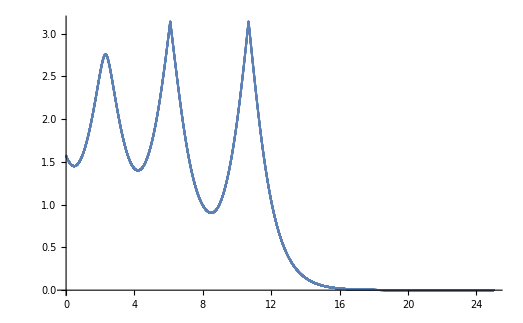

```mathematica
ListPlot[Table[{n*Δt ,Subscript[θ, RK4][n]},{n,0,nMAX}]]
```

### variação θ’[n] com o tempo

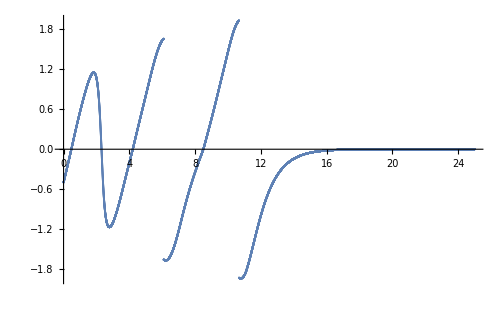

```mathematica
ListPlot[Table[{n*Δt ,Subscript[θ, RK4]'[n]},{n,0,nMAX}]]
```

### Variação de ϕ’[n] com o tempo

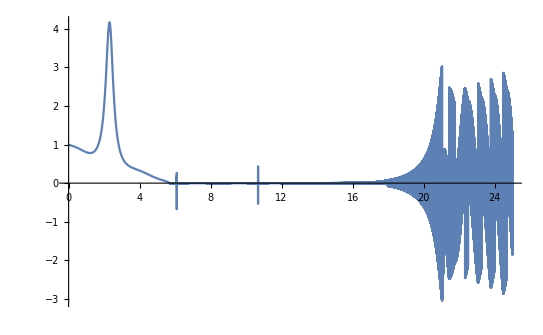

```mathematica
ListPlot[Table[{n*Δt ,Subscript[ϕ, RK4]'[n]},{n,0,nMAX}],PlotRange->All,Joined->True]
```

### Aceração do pivot ao longo do tempo

```mathematica
Animate[ListPlot[Table[{ax[n],ay[n]},{n,0,n1,10}]],{n1,0,nMAX,10},DefaultDuration->30,AnimationRunning->False]
```

### Posição do Pivot ao longo do tempo

```mathematica
Animate[ListPlot[Table[{Subscript[x1, RK4][n],Subscript[y1, RK4][n]},{n,0,n1,10}]],{n1,0,nMAX,10},DefaultDuration->30,AnimationRunning->False]
```